# 25: Eigenvalue Algorithms:

We know that we can not use the Characteristic Polynomial to compute eigenvalues. The question is how do we compute all the eigenvalues or more generally the eigen decomposition of a matrix A.

## Localization Pic Code

```mathematica
GershgorignPic[A_]:=Module[{m=Length[A],c,r},
Graphics[{
Table[
c=ReIm[A⟦i,i⟧];
r1=Sum[Abs[A⟦i,j⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
r2=Sum[Abs[A⟦j,i⟧],{j,1,i-1}]+Sum[Abs[A⟦i,j⟧],{j,i+1,m}];
{Hue[i/m],Opacity[0.2],EdgeForm[Hue[i/m]],
Disk[c,Min[r1,r2],{0,π/2}],
Disk[c,Min[r1,r2],{π/2,π}],
Disk[c,Min[r1,r2],{π,3π/2}],
Disk[c,Min[r1,r2],{3π/2,2π}]},
{i,m}],
Point[ReIm[Eigenvalues[A]]]},
Frame->True,
GridLines->Automatic]
]
```

## Companion Polynomials

Matlab computes polynomial roots by building a matrix which has the same roots.  There are actually a whole bunch of these companion matrices for a given polynomial. The most common is implemented below

```mathematica
CompanionMatrix[a_]:= Module[{m=Length[a],A},
A=SparseArray[{Band[{2,1}]->1},{m-1,m-1}];
A⟦All,m-1⟧=-a⟦1;;-2⟧/a⟦-1⟧;
A
]
```

```mathematica
p[x_]:=2 x^2+3x +1 + x^7
a=CoefficientList[p[x], x];
A=CompanionMatrix[a];
MatrixForm[A];
Sort[Eigenvalues[N[A]]]
Sort[x/.NSolve[p[x]==0,x]]
```

{-0.794993-0.359485 ⅈ,-0.794993+0.359485 ⅈ,-0.493017+0. ⅈ,-0.106686-1.20568 ⅈ,-0.106686+1.20568 ⅈ,1.14819-0.707374 ⅈ,1.14819+0.707374 ⅈ}

{-0.794993-0.359485 ⅈ,-0.794993+0.359485 ⅈ,-0.493017,-0.106686-1.20568 ⅈ,-0.106686+1.20568 ⅈ,1.14819-0.707374 ⅈ,1.14819+0.707374 ⅈ}

## Theorem 25.1: Galois

We all know the quadratic formula for the roots of a λ^2+b λ+c =0. There is a formula for the three roots of a cubic.  Here is one version!

```mathematica
Clear[a,b,c,λ]
λ/.Solve[λ^3+a λ^2+b λ+c==0,λ]
```

There is a much longer formula for the four roots of a quartic

```mathematica
Clear[a,b,c,d,λ]
λ/.Solve[λ^4+a λ^3+b λ^2+c λ +d==0,λ]
```

Abel proved in 1824 that no such general formula can exist for higher degree polynomials!  See Theorem 25.1 for a careful statement of the theorem. What this means is that algorithms to compute eigenvalues need to be iterative like Newton’s method!

## Iterative Schemes

Iterative schemes have some advantages

Black-box algorithms only use the matrix rather than work on the matrix.  This is essential to exploit sparsity! It also means they do not need to compute all the eigenvalues. Maybe you only care about the big ones!

You do not have to wait for full convergence if a “rough” answer will do.

Here are a couple of iterative algorithms.

### Oldest Eigenvalue Algorithm: Jacobi

Before the word “matrix” existed Jacobi needed to compute what would be called the eigenvalues of a real symmetric 7×7 matrix: there were only seven known planets at the time! He invented what is now called the Jacobi method!

#### Background and Code

We can diagonalize a symmetric 2 by 2 matrix using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a12, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a12 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a12 p2)+p1 (a12 p1+a22 p2)
p1 (a12 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a12 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work for any p2! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦1,2⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12^2-2 a11 a22+a22^2) p2)/(2 a12)}}

It is OK since a11^2+4 a12^2-2 a11 a22+a22^2=(a11-a22)^2+4 a12^2.  In practice, we should choose which solution we use carefully.  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMat[{{a11_,a12_},{a21_,a22_}}]:=Module[{p1,p2=1},
p1=(a11-a22-√((a11-a22)^2+4 a12^2))/(2 a12);
{p1,p2}=Normalize[{p1,p2}];
({{p1, p2}, {-p2, p1}})
]
```

As always test

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
G=JMat[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}];
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

-Graphics-

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJ,HoldFirst];
BigJ[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMat[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
m=7;
A=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
{i,j}={1,5};
G=BigJ[A,{i,j}];
GAGt=G.A.Gᵀ;
TabView[Map[MatrixPlot,Chop[{GAGt,G,G.Gᵀ,A}]]]
```

1234

So lets try to string a few of these together. It works just the way we expect if we are careful not to overlap!

```mathematica
m=7;
A=A0=RandomReal[{-1,1},{m,m}]; A= A + Aᵀ;
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{3,4},{5,6}}}];
SetOptions[MatrixPlot, 
ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
```

123

If we overlap zeros that were made earlier get messed up.

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0
Data=Table[
G=BigJ[A,ij];
A=G.A.Gᵀ,
{ij,{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7}}}];
SetOptions[MatrixPlot, ColorRules->{0->Green},Mesh->All,MeshStyle->Red];
TabView[Map[MatrixPlot,Chop[Data]]]
MatrixForm[A]
```

{{-0.080919,0.583283,-0.683814,0.377432,-0.509303,-0.942687,1.08742},{0.583283,1.69082,0.753464,0.575205,1.42253,-0.510261,-0.938563},{-0.683814,0.753464,0.770462,0.049387,1.00186,0.892969,0.847836},{0.377432,0.575205,0.049387,1.65438,-0.870101,-1.68322,-0.447118},{-0.509303,1.42253,1.00186,-0.870101,0.983722,0.543581,0.138338},{-0.942687,-0.510261,0.892969,-1.68322,0.543581,0.862603,1.21398},{1.08742,-0.938563,0.847836,-0.447118,0.138338,1.21398,-0.687621}}

123456

(-2.3469 | 0.653997 | 0.0614361 | 0.137845 | 0.0374645 | 0.834888 | 1.19979×10^-17
0.653997 | 1.86561 | 0.456196 | 0.678132 | 1.18377 | 0.762214 | -0.183978
0.0614361 | 0.456196 | 1.26854 | -0.0544363 | 1.30494 | -1.14936 | 0.178252
0.137845 | 0.678132 | -0.0544363 | 1.67007 | -0.883674 | 1.69402 | -0.312744
0.0374645 | 1.18377 | 1.30494 | -0.883674 | 1.00856 | -0.548954 | -0.0322495
0.834888 | 0.762214 | -1.14936 | 1.69402 | -0.548954 | 0.862715 | -0.863129
2.22045×10^-16 | -0.183978 | 0.178252 | -0.312744 | -0.0322495 | -0.863129 | 0.864853)

Jacobi (or more likely one of his helpers aka computers or computes) was doing this by hand and would have been painstakingly updating a block of numbers.

You would like to be done as fast as possible.

You can do any of the entries.

Which one should you do?

Jacobi’s plan was “do the big ones first!”  This assumes that arithmetic is slow (it was then) and that it is fast (true for a small matrix) to find the biggest entry.

```mathematica
SetAttributes[JacobiStep, HoldFirst]
JacobiStep[A_]:= Module[{AbsA=Abs[UpperTriangularize[A,1]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Position[AbsA,Max[AbsA]]⟦1⟧;
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJ[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

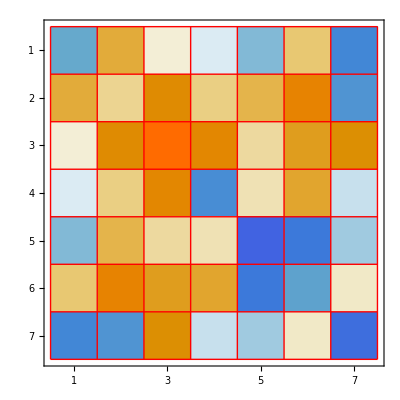
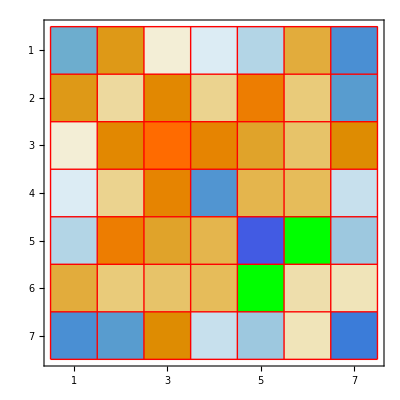

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
JacobiStep[A]
Map[MatrixPlot,Chop[{A0,A}]]
```

Now we can do a bunch and know that we are always targeting (and zeroing) large entries! This ensures it always makes progress and that it converges fast at the end!  Of course, copying and pasting is not a good plan! After a few steps the off-diagonal is looking fairly pale!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
TabView[{
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]],
JacobiStep[A];MatrixPlot[Chop[A]]}]
```

12345678

Automation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=16;
TabView[Table[
JacobiStep[A];MatrixPlot[Chop[A]],
{MaxIter}]]
```

12345678910111213141516

#### Demo

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}]; A0= A0 + A0ᵀ;
A=A0;
MaxIter=89;
ListAnimate[Table[
JacobiStep[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

This algorithm has more parallelism the standard “QR” Francis algorithm we are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up”.

### Power Method: A Simple Iterative Scheme

There is a simple way to compute the eigenvector associated with the largest eigenvalue of almost any matrix A. In words, multiply by A and normalize repeatedly.  This is very easy to code.

```mathematica
PowerMethod[A_][x_]:=Module[{z=A.x},z/Norm[z]]
```

It works!  Here is a simple test on an SPD matrix.

```mathematica
m=6;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
x0=RandomReal[{-1,1},m];
TableForm[PowerMethodData=NestList[PowerMethod[A], x0,34],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6
1 | -0.873225 | -0.406332 | 0.16695 | -0.933622 | 0.773505 | 0.648259
2 | -0.131065 | 0.024428 | 0.573991 | -0.668112 | 0.454083 | -0.0139351
3 | -0.150558 | 0.0962248 | 0.579449 | -0.668642 | 0.412936 | -0.121305
4 | -0.213073 | 0.136111 | 0.563459 | -0.65226 | 0.395661 | -0.191306
5 | -0.271651 | 0.164654 | 0.544045 | -0.628921 | 0.378807 | -0.253125
6 | -0.321494 | 0.186457 | 0.523094 | -0.602937 | 0.361709 | -0.306402
7 | -0.362381 | 0.203349 | 0.502238 | -0.577034 | 0.345222 | -0.350628
8 | -0.395203 | 0.216437 | 0.482717 | -0.552888 | 0.330068 | -0.386424
9 | -0.421214 | 0.226556 | 0.465238 | -0.53136 | 0.31665 | -0.414963
10 | -0.44169 | 0.234372 | 0.450066 | -0.512742 | 0.305088 | -0.437535
11 | -0.457767 | 0.240416 | 0.437182 | -0.496978 | 0.29532 | -0.455324
12 | -0.470389 | 0.245101 | 0.426409 | -0.483825 | 0.287182 | -0.469334
13 | -0.48031 | 0.248745 | 0.417498 | -0.472967 | 0.280471 | -0.480377
14 | -0.488125 | 0.25159 | 0.410187 | -0.464069 | 0.274976 | -0.489093
15 | -0.494294 | 0.253819 | 0.404221 | -0.456817 | 0.270501 | -0.495986
16 | -0.499175 | 0.255571 | 0.399375 | -0.45093 | 0.266869 | -0.501448
17 | -0.503045 | 0.256954 | 0.39545 | -0.446166 | 0.263931 | -0.505783
18 | -0.506118 | 0.258047 | 0.392278 | -0.442318 | 0.261559 | -0.50923
19 | -0.508563 | 0.258914 | 0.38972 | -0.439216 | 0.259647 | -0.511975
20 | -0.510511 | 0.259602 | 0.38766 | -0.436718 | 0.258108 | -0.514162
21 | -0.512064 | 0.26015 | 0.386002 | -0.434709 | 0.25687 | -0.515908
22 | -0.513303 | 0.260587 | 0.38467 | -0.433094 | 0.255875 | -0.517301
23 | -0.514294 | 0.260935 | 0.383599 | -0.431797 | 0.255076 | -0.518415
24 | -0.515086 | 0.261213 | 0.382739 | -0.430755 | 0.254434 | -0.519306
25 | -0.515719 | 0.261435 | 0.382049 | -0.429919 | 0.253919 | -0.520019
26 | -0.516225 | 0.261613 | 0.381495 | -0.429248 | 0.253506 | -0.520589
27 | -0.516631 | 0.261755 | 0.38105 | -0.42871 | 0.253175 | -0.521045
28 | -0.516955 | 0.261868 | 0.380694 | -0.428278 | 0.252909 | -0.521411
29 | -0.517215 | 0.261959 | 0.380408 | -0.427932 | 0.252696 | -0.521703
30 | -0.517424 | 0.262032 | 0.380179 | -0.427655 | 0.252525 | -0.521938
31 | -0.51759 | 0.262091 | 0.379995 | -0.427432 | 0.252388 | -0.522125
32 | -0.517724 | 0.262137 | 0.379848 | -0.427254 | 0.252278 | -0.522276
33 | -0.517831 | 0.262175 | 0.37973 | -0.427111 | 0.25219 | -0.522396
34 | -0.517917 | 0.262205 | 0.379635 | -0.426996 | 0.252119 | -0.522493
35 | -0.517986 | 0.262229 | 0.379559 | -0.426904 | 0.252062 | -0.52257

It has almost converged to the eigenvector associated with the largest eigenvalue!

```mathematica
Eigensystem[A,1]
```

{{3.55898},{{0.518263,-0.262326,-0.379252,0.426533,-0.251834,0.522883}}}

## Much Newer: Non Symmetric Jacobi

#### 2×2 Diagonalization

We can make a general 2 by 2 matrix upper triangular using the Givens rotation (p1 | p2
-p2 | p1).   Lets work out the recipe!

```mathematica
AHat=({{p1, p2}, {-p2, p1}}).({{a11, a12}, {a21, a22}}).({{p1, -p2}, {p2, p1}});
MatrixForm[AHat]
```

(p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2) | -p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)
p1 (a21 p1-a11 p2)+p2 (a22 p1-a12 p2) | -p2 (a21 p1-a11 p2)+p1 (a22 p1-a12 p2))

There are two values of p1 that work for any p2! Of course, we need to check that the expression under the square root is not negative if we want a real computation.

```mathematica
Solve[AHat⟦2,1⟧==0,p1]
```

{{p1→(a11 p2-a22 p2-√(a11^2+4 a12 a21-2 a11 a22+a22^2) p2)/(2 a21)},{p1→(a11 p2-a22 p2+√(a11^2+4 a12 a21-2 a11 a22+a22^2) p2)/(2 a21)}}

#### xxx

```mathematica
Simplify[AHat⟦1,1⟧]
Simplify[AHat⟦1,2⟧]
Hmm=D[AHat⟦1,1⟧+AHat⟦1,2⟧,{{p1,p2}}]
Hmm=Normal[CoefficientArrays[Hmm,{p1,p2}]⟦2⟧];
MatrixForm[Hmm]
```

a11 p1^2+p2 (a12 p1+a21 p1+a22 p2)

-p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)

{2 a11 p1+2 a12 p1-a11 p2+a12 p2+a21 p2+a22 p2,-a11 p1+a12 p1+a21 p1+a22 p1-2 a21 p2+2 a22 p2}

(2 a11+2 a12 | -a11+a12+a21+a22
-a11+a12+a21+a22 | -2 a21+2 a22)

```mathematica
{{Simplify[p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2), -p2 (a11 p1+a21 p2)+p1 (a12 p1+a22 p2)}}]
```

Syntax::bktmop: Expression "Simplify[p1(a11p1+a21p2)+p2(a12p1+a22p2) | -p2(a11p1+a21p2)+p1(a12p1+a22p2)]" has no opening "[".

#### xxx

It would be OK if a11^2+4 a12*a21-2 a11 a22+a22^2=(a11-a22)^2+4 a12*a21 is positive. Conditions like this are unavoidable.  Non-symmetric matrices can have complex eigenvalues which are non diagonalizable with real rotations!

An alternative would be to make the bottom entry as small as possible!  It turns out it is easier to make the 11 entry as large (in absolute value) as possible. We want to maximize 
	f[{p1,p2}]=p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2) 
subject to 
	g({p1,p2}]=p1^2+p2^2==1
This is just a standard Lagrange Multiplier problem.  If you go back and look in your calculus book you find that we want to find p satisfying||p||=1and 
	∇f(p)=λ ∇g(p)
Computing the derivatives is simple ∇g(p)=2p and ∇f(p)=B.p where 
	B=2(a_11 | 0.5(a_12+a_21)
0.5(a_12+a_21) | a_22) 
If we write p=v this looks familiar since we need to solve B.v=λ v  with ||v||=1.  It is a symmetric eigenvalue problem!  The eigenvector associated with the biggest eigenvalue gives the maximum and the smallest eigenvector gives the minimum.

```mathematica
MatrixForm[D[p1 (a11 p1+a21 p2)+p2 (a12 p1+a22 p2),{{p1,p2}}]]
```

(2 a11 p1+a12 p2+a21 p2
a12 p1+a21 p1+2 a22 p2)

In practice, we should choose which solution we use carefully.  The  For now I am going to use the first one! Remember for the Givens matrices we need ||{p1,p2}||=1.

```mathematica
JMatNonSym[{{a11_,a12_},{a21_,a22_}}]:=Module[{a,p1,p2},
a=0.5(a12+a21);
{p1,p2}=Eigenvectors[({{a11, a}, {a, a22}}),1]⟦1⟧;
({{p1, p2}, {-p2, p1}})
]
```

As always test

{(1. | 0.
0. | 1.),(-1.33031 | 0.0598579
-0.0598579 | -0.194927)}

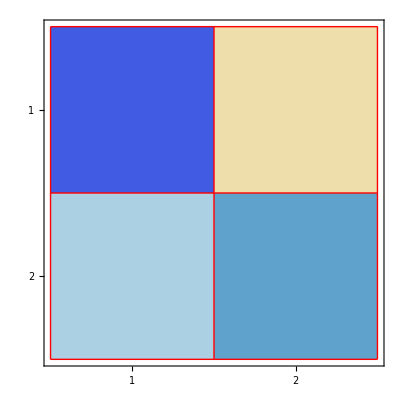

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
G=JMatNonSym[A];
GAGt=G.A.Gᵀ;
Map[MatrixForm,{G.Gᵀ,GAGt}]
MatrixPlot[Chop[GAGt],PlotLegends->Automatic]
```

To use this in a larger matrix we target a specific entry {i,j} and embed the appropriate tiny rotation in the identity matrix.

```mathematica
SetAttributes[BigJMatNonSym,HoldFirst];
BigJMatNonSym[A_,{i_,j_}]:=Module[{m=Length[A],G},
G=IdentityMatrix[m];
G⟦{i,j},{i,j}⟧=JMatNonSym[A⟦{i,j},{i,j}⟧];
G
]
```

As always test!

```mathematica
SetAttributes[JacobiStepNonSym, HoldFirst]
JacobiStepNonSym[A_]:= Module[{AbsA=Abs[LowerTriangularize[A,-2]],ij,G},
(* Find the largest non-diagonal entry *)
ij=Reverse[Position[AbsA,Max[AbsA]]⟦1⟧];
(* Compute the Jacobi/Given rotation zapping the biggest entry *)
G=BigJMatNonSym[A,ij];
(* Update A in place *)
A=G.A.Gᵀ;
(* No need to return anything! *)
]
```

As always test.

Animation is a good thing!

```mathematica
m=7;
A0=RandomReal[{-1,1},{m,m}];
A=A0;
MaxIter=223;
ListAnimate[Table[
JacobiStepNonSym[A];MatrixPlot[Chop[A],PlotLabel->i],
{i,MaxIter}],8]
```

```mathematica
MatrixForm[A0]
MatrixForm[A]
```

(-0.686361 | 0.94498 | 0.253141 | -0.958761 | -0.409283 | 0.417068 | 0.83985
0.619882 | 0.831056 | 0.0477851 | 0.999053 | 0.163265 | -0.990303 | 0.700778
0.29804 | -0.413416 | 0.591357 | -0.807766 | 0.403721 | 0.590652 | -0.098909
-0.0394445 | -0.728158 | -0.422137 | 0.937795 | 0.411594 | -0.706274 | 0.353326
0.746242 | -0.705333 | 0.979705 | 0.428487 | 0.318967 | -0.244213 | 0.094919
0.443905 | 0.285225 | -0.183931 | -0.202565 | -0.487426 | 0.432355 | 0.387248
-0.725657 | -0.917695 | 0.00836931 | -0.529171 | 0.851881 | -0.115383 | -0.930074)

(-0.686361 | 0.896142 | 0.0644286 | 0.269337 | 0.476909 | 0.417068 | 1.28138
-0.686335 | -0.936728 | -0.555114 | 0.848094 | -0.657311 | -0.17581 | -0.39203
-0.704175 | 0.0630675 | 1.16016 | -0.728364 | -0.287992 | -0.301106 | 0.422217
-0.350059 | -0.718233 | 0.00875979 | 1.03697 | 0.510911 | 1.14285 | 0.889005
-0.387095 | -0.118599 | 0.287992 | 0.522464 | -0.249832 | 0.563777 | 0.723529
0.443905 | 0.403988 | 0.451653 | 0.0150746 | 0.259663 | 0.432355 | 0.330021
0.564615 | 0.483646 | -0.124538 | -0.889005 | 0.292392 | -0.394755 | 0.738533)

Things to note, something about our choices is pushing the negative eigenvalues up and the positive eigenvalues down!  Other choices will do other things! The common choice is to push the big (either positive or negative eigenvalues up) and the small eigenvalues down!

This algorithm has more parallelism the standard “QR” Francis algorithm we are going to learn.  It has a developed very quaternionic G4 version that block diagonalizes symmetric matrices.  I am working on an alternative G4 and a G8 algorithm that make progress with a simple plan of “move the big entries up”.

It is common for

## Preliminary Hessenberg Reduction

For now we are going to look at classical dense matrix eigenvalue algorithms which start with a reduction very similar to a QR decomposition and then iterates to reveal all the eigenvalues of a dense matrix.

We are going to look and see what the first step does before we learn how to do it!

### Symmetric Matrix⟶Tri-Diagonal⟶^(k→∞)Diagonal

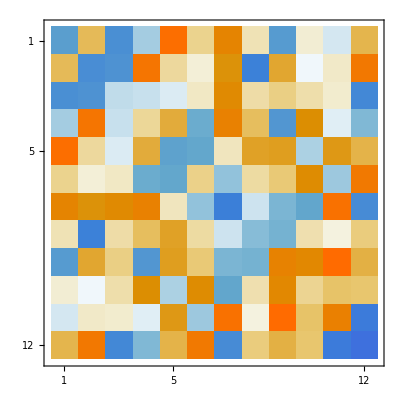
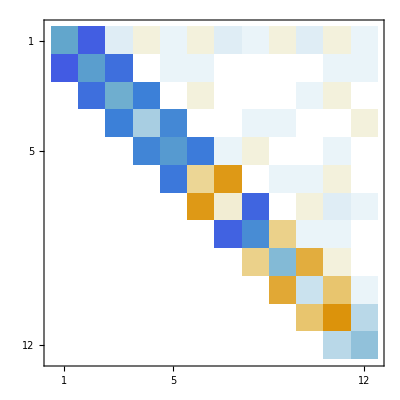
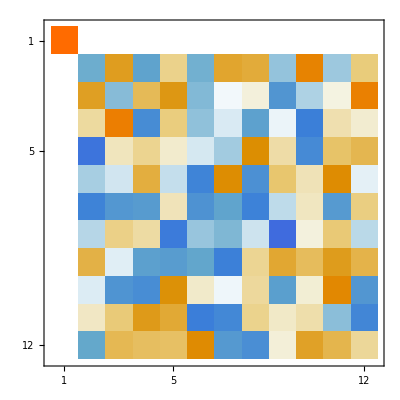

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
{Q,T}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,T,Q}]
```

```mathematica
TabView[{"A"->GershgorignPic[A],"T"->GershgorignPic[T]}]
```

12

The tridiagonal matrix give tighter bounds. If we could make it more diagonal we would be able to isolate the eigenvalues.  This is the plan.  For symmetric matrices we are going to work out how to make the tridiagonal matrix more diagonal.

### General Matrix⟶Almost Upper Triangular⟶^(k→∞)UT

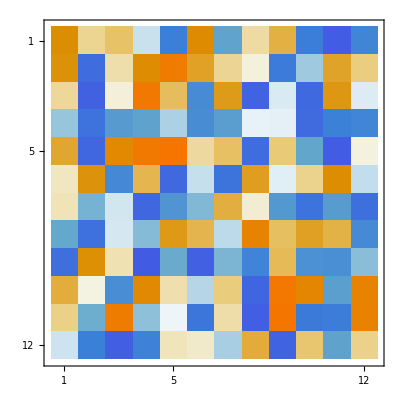
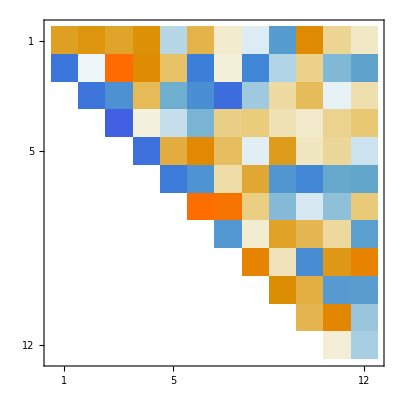
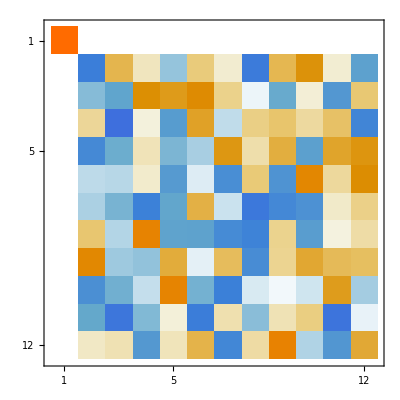

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; 
{Q,H}=HessenbergDecomposition[A];
Map[MatrixPlot,{A,H,Q}]
```

```mathematica
TabView[{"A"->GershgorignPic[A],"H"->GershgorignPic[H]}]
```

12

The almost upper triangular matrix give tighter bounds. If we could make it more upper triangular we would be able to isolate the eigenvalues.  This is the plan.  For general matrices we are going to work out how to make the almost upper triangular matrix more upper triangular.